```mathematica
n=1.0008; (*gas*)
```

```mathematica
n=1.02; (*aerogel*)
```

maximum cherenkov angle [mrad]

198.355

minimum momentum for cherenkov emission

{e,pi,K,p}

{0.00253734,0.694038,2.47764,4.66672}

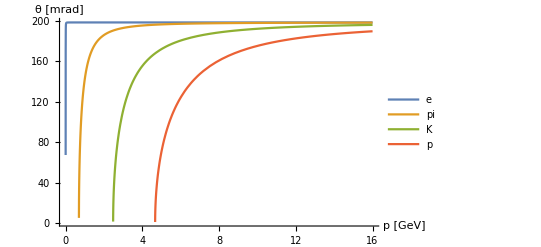

```mathematica
masslist={0.00051,0.1395,0.498,0.938};
partlist={"e","pi","K","p"};
Print["maximum cherenkov angle [mrad]"]
1000*ArcCos[1/n]
Print["minimum momentum for cherenkov emission"]
partlist
Evaluate[Table[m/Sqrt[n^2-1],{m,masslist}]]
(* cherenkov cone angle vs momentum *)
Plot[Evaluate[Table[
1000*ArcCos[Sqrt[p^2+m^2]/(n*p)],
{m,masslist}
]],{p,0,16},
AxesLabel->{"p [GeV]","θ [mrad]"},
PlotRange->All,
PlotLegends->partlist
]
```